```mathematica
LX1 = {{0,123},{100,123},{200,122},{350,121},{400,120},{425,112.7},{450,102.9},{475,101},{500,92.1},{550,72.4},{575,60.7},{600,52.7},{650,33.5},{700,15.8},{750,0.745},{800,0.304},{850,0.000104},{900,0.000576},{950,0.000297},{1000,0.00016}};
LX2 = {{0,111.1},{100,110.4},{200,100.2},{250,92},{300,82.3},{350,72},{400,62.1},{450,52.5},{500,44.1},{550,32.4},{600,21.7},{650,5.75},{700,1.58},{750,0.8712},{800,0.65},{900,0.257},{1000,0.00002}};
LX3={{0,103},{100,99.2},{200,82.9},{250,73.1},{300,68.7},{350,65},{400,58.2},{450,52.5},{500,45.8},{550,39.6},{600,37},{700,21},{800,12.3},{900,1.52},{1000,0.000052}};
```

```mathematica
CX1 = {{0,7.75},{200,7.72},{300,7.69},{450,7.52},{475,6.85},{500,3.46},{525,0.754},{550,0.129},{575,0.000073},{600,0.000065},{700,0.000021},{800,0.000005}};
CX2 = {{0,7.36},{100,7.35},{300,7.3},{350,5.67},{375,2.92},{400,0.832},{450,0.00000068},{500,0.00000035}};
CX3 = {{0,7.29},{100,7.29},{200,7.29},{300,7.26},{350,7.17},{400,6.58},{450,4.29},{475,2.56},{500,1.31},{550,0.21},{600,0.000046},{650,0.000019}};
```

```mathematica
FLX1 = NonlinearModelFit[LX1,P1+.5*P*(Erf[w*(x-x1)]),{{P,123},{P1,150},{w,.01},{x1,500}},x]
FLX2 = NonlinearModelFit[LX2,P1+.5*P*(Erf[w*(x-x1)]),{{P,123},{P1,150},{w,.01},{x1,500}},x]
FLX3= NonlinearModelFit[LX3,P1+.5*P*(Erf[w*(x-x1)]),{{P,123},{P1,150},{w,.01},{x1,500}},x]
```

FittedModel[60.8892-62.1632 Erf[0.00634296 (-577.044+x)]]

FittedModel[54.9086-57.9552 Erf[0.00366724 (-433.866+x)]]

FittedModel[60.7333-81.0895 Erf[0.00138689 (-378.784+x)]]

```mathematica
FCX1 = NonlinearModelFit[CX1,P1+.5*P*(Erf[w*(x-x1)]),{{P,9},{P1,150},{w,.01},{x1,500}},x]
FCX2 = NonlinearModelFit[CX2,P1+.5*P*(Erf[w*(x-x1)]),{{P,9},{P1,150},{w,.01},{x1,300}},x]
FCX3 = NonlinearModelFit[CX3,P1+.5*P*(Erf[w*(x-x1)]),{{P,9},{P1,150},{w,.01},{x1,500}},x]
```

FittedModel[3.86318-3.83519 Erf[0.035892 (-497.88+x)]]

FittedModel[3.67599-3.67147 Erf[0.0278502 (-368.65+x)]]

FittedModel[3.64219-3.62713 Erf[0.0159368 (-459.025+x)]]

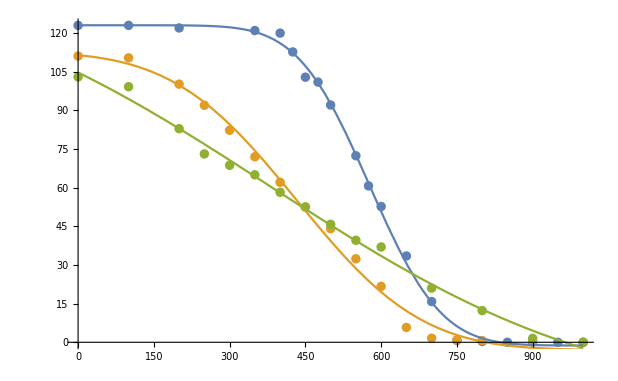

```mathematica
Show[ListPlot[{LX1,LX2,LX3}],Plot[{FLX1[x],FLX2[x],FLX3[x]},{x,0,1000}]]
```

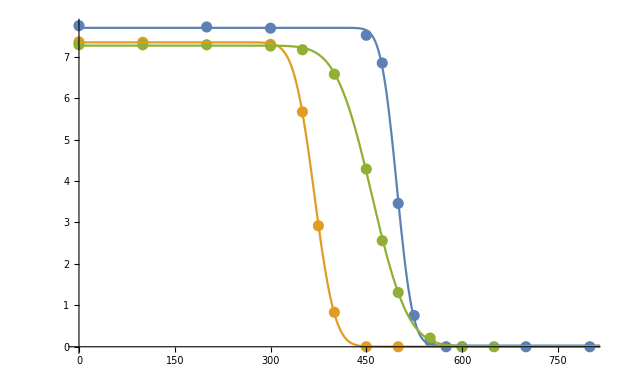

```mathematica
Show[ListPlot[{CX1,CX2,CX3}],Plot[{FCX1[x],FCX2[x], FCX3[x]},{x,0,1000}]]
```

```mathematica
LY1 = {{0,123},{100,121},{200,121},{225,116.7},{250,102.3},{260,87.3},{270,71},{280,52.7},{290,37.2},{300,25.4},{325,8.28},{350,2.99},{400,1.2},{450,0.777},{550,0.358},{600,0.241},{700,0.000653}};
LY2 = {{0,112},{100,111.2},{200,101.1},{250,80.2},{300,49.6},{350,21.6},{400,6.47},{450,1.72},{500,0.567},{550,0.316},{600,0.263}};
LY3={{0,103},{100,103},{200,102.3},{300,96.6},{400,62.7},{450,45.6},{500,30.4},{600,12.5}};
```

```mathematica
CY1 = {{0,7.74},{100,7.73},{200,7.69},{300,5.74},{310,4.24},{325,1.89},{350,0.429},{400,0.000084},{500,0.000041},{600,0.000026}};
CY2 = {{0,7.35},{100,7.35},{200,7.33},{300,6.04},{325,3.41},{350,1.17},{400,0.000057},{450,0.000039}};
CY3 = {{0,7.3},{100,7.3},{200,7.3},{300,7.28},{400,7.2},{500,5.18},{550,1.94},{600,0.338},{650,0.000055},{700,0.000025}};
```

```mathematica
FLY1 = NonlinearModelFit[LY1,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,123},{P1,150},{w,.01},{x1,500}},x]
FLY2 = NonlinearModelFit[LY2,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,123},{P1,150},{w,.01},{x1,500}},x]
FLY3 = NonlinearModelFit[LY3,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,123},{P1,150},{w,.01},{x1,500}},x]
```

FittedModel[61.5062-60.3534 Erf[1+0.0252088 (-315.398+x)]]

FittedModel[56.086-55.7026 Erf[1+0.0102454 (-387.315+x)]]

FittedModel[57.106+46.3384 Erf[1-0.00759303 (-288.202+x)]]

```mathematica
FCY1 = NonlinearModelFit[CY1,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,9},{P1,150},{w,.01},{x1,500}},x]
FCY2 = NonlinearModelFit[CY2,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,9},{P1,150},{w,.01},{x1,300}},x]
FCY3 = NonlinearModelFit[CY3,P1+.5*P*(Erf[1-w*(x-x1)]),{{P,9},{P1,150},{w,.01},{x1,500}},x]
```

FittedModel[3.88699+3.83669 Erf[1-0.0371539 (-285.218+x)]]

FittedModel[3.67751+3.67163 Erf[1-0.0272929 (-286.584+x)]]

FittedModel[3.64603+3.63399 Erf[1-0.0164848 (-462.937+x)]]

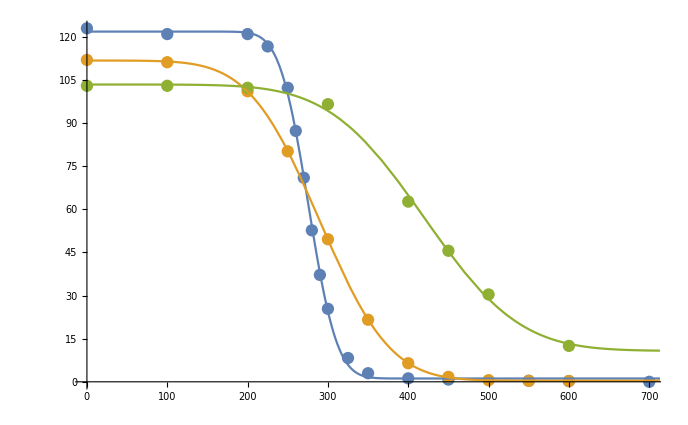

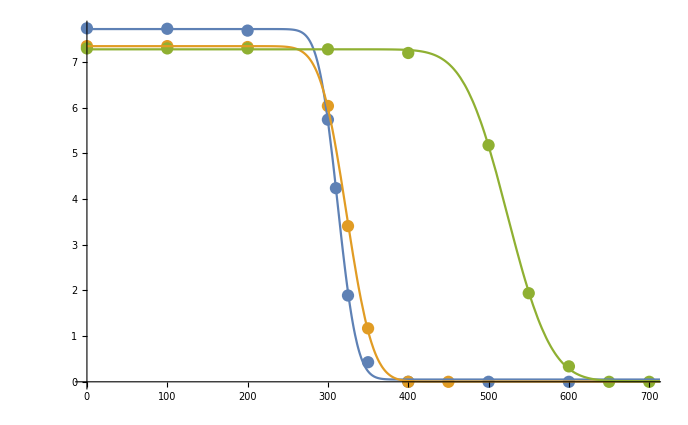

```mathematica
Show[ListPlot[{LY1,LY2,LY3}],Plot[{FLY1[x],FLY2[x],FLY3[x]},{x,0,1000}]]
Show[ListPlot[{CY1,CY2,CY3}],Plot[{FCY1[x],FCY2[x],FCY3[x]},{x,0,1000}]]
```